```mathematica
NS["fmri_alzheimer_reduction"]
```

```mathematica
(* definition of empirical covariance matrix, used a lot in the following *)covmatrix[data_]:=Block[{means=Mean@T@data,numindividuals=Length[data[[1]]]},
((data-means).T[data-means])/numindividuals]
```

```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\nanunana\\data170629"]
```

C:\Users\pglpm\repositories\nanunana\data170629

```mathematica
categories={"modafinil","placebo"};
categoryfiles={"test_modafinil_M.txt", "test_modafinil_P.txt"};
numcategories=Length[categories];
quantities=Flatten@Import["quantities.txt","CSV"];
numquantities=Length@quantities;

Do[subjectfile[ii]=Import[categoryfiles[[ii]],"CSV"];numindividuals[ii]=Length[subjectfile[ii][[1]]],
{ii,numcategories}];
(* one row for each quantity, one column for each individual *)
minnumindividuals=Min@Table[numindividuals[ii],{ii,numcategories}];
```

```mathematica
minnumindividuals
```

13

```mathematica
numquantities
```

24

```mathematica
(* renormalize data for numerical stability *)

(* collect all data from all categories first *)
totaldata={};Do[totaldata=Join[totaldata,T[subjectfile[ii]]],{ii,numcategories}];
 (* individuals are in one column *)

tempmeans=Mean@totaldata;tempstds=Std@totaldata;
totaldata=(T@totaldata-tempmeans)/tempstds;

(* now renormalize and standardize *)
Do[subjectfile[ii]=(subjectfile[ii]-tempmeans)/tempstds,{ii,numcategories}]
```

```mathematica
(* a look at the eigenvectors and eigenvalues of the empirical covariance matrix *)
T@Eigensystem[covmatrix[T@totaldata]]//MF
```

(16.7263 | {0.232497,-0.0489996,-0.36019,0.201038,0.195593,-0.263086,0.0879188,0.151966,-0.208707,-0.109359,0.0762281,0.206831,-0.0427949,-0.0325863,0.165919,0.258084,-0.161243,-0.0975018,0.282271,0.0119689,-0.0980486,-0.335477,-0.0572707,0.196075,-0.373774,0.12265}
3.5631 | {0.0110363,-0.155049,0.233133,0.00273212,-0.0804033,0.0756706,0.00412005,0.449972,0.290143,0.116789,-0.0491941,-0.0255642,-0.0984503,-0.287075,-0.0859501,0.0195909,0.053964,-0.0193049,-0.00544427,0.108096,-0.310927,-0.565663,0.0043078,0.0173821,0.270968,0.0251194}
1.66791 | {0.149982,-0.229115,0.312806,0.220127,0.0985118,-0.0329109,-0.116327,-0.358203,0.277835,-0.279724,-0.0670062,0.0842226,-0.0751205,-0.181265,0.061381,0.1701,-0.0689353,-0.37633,0.340062,0.0227241,-0.151225,0.241019,-0.0958343,-0.00538106,0.158594,-0.0999869}
1.35722 | {0.00809781,-0.083301,-0.0629894,-0.00863292,0.000335859,-0.227712,-0.0946887,0.719085,-0.0722409,-0.107619,-0.0616377,-0.000400502,-0.0578375,0.0334969,-0.0504669,-0.0191002,-0.172185,-0.181318,-0.0307607,-0.0164689,0.0360666,0.518435,-0.141423,0.00490086,0.150145,-0.0817803}
0.544261 | {-0.0910866,0.00872453,-0.204138,0.170022,-0.00632914,-0.384155,-0.0798826,-0.0468896,0.4076,-0.059753,0.14125,-0.11292,0.24555,0.17493,0.0285392,-0.239717,-0.115693,-0.254313,-0.139774,0.433812,0.212579,-0.156605,0.186128,-0.149894,0.0243336,0.00768244}
0.191238 | {0.134027,-0.0779415,-0.337731,-0.0775787,0.0411526,-0.265337,0.0729355,-0.228292,-0.0187383,0.13775,-0.0522955,-0.192262,-0.162577,-0.0603033,-0.00900041,0.0926227,-0.23676,0.376093,0.0707305,0.11009,-0.165302,0.105796,-0.0579086,-0.0170868,0.545547,0.27237}
0.104976 | {0.0523575,-0.14747,-0.317944,0.190778,-0.214872,0.293774,-0.192604,-0.0194417,-0.199334,0.363409,0.0280166,-0.0175808,-0.037459,-0.314591,-0.11862,0.0110461,0.105332,-0.26663,0.0361267,0.24042,-0.111591,0.219314,0.411347,0.00674879,-0.06928,0.0687474}
0.0839205 | {0.193016,0.0538906,0.127186,-0.0624224,0.104349,-0.024317,-0.51388,0.0060159,-0.382472,0.0667961,0.0503275,-0.0770708,0.0139505,0.168291,-0.0202882,0.111755,-0.0291033,-0.166014,0.153166,-0.132018,0.37231,-0.302712,0.124156,-0.120637,0.358743,-0.0730177}
0.0530603 | {0.113526,-0.133804,0.294561,-0.257524,0.214065,-0.183345,0.148573,-0.0941511,-0.232186,0.0399876,0.294265,0.0883373,-0.0152025,-0.0709167,0.11413,-0.039962,-0.0179483,-0.326406,-0.496239,-0.002285,-0.144332,0.0450915,0.128425,0.139103,0.0447764,0.349463}
0.01555 | {-0.0100779,-0.00780541,-0.316256,-0.335178,0.183901,0.335253,0.0911814,0.107681,0.224006,-0.333374,-0.0392014,0.000156617,-0.0975613,0.00363829,0.302549,0.0627439,-0.033511,-0.127952,0.0346398,-0.22898,-0.00170834,-0.0134254,0.359197,-0.362238,0.0739725,0.128349}
0.0130547 | {-0.133344,0.0901029,-0.109019,0.300257,0.326753,0.264815,-0.152865,-0.000823847,-0.195806,-0.229719,0.144407,0.150299,0.363047,-0.276957,0.124575,-0.286176,-0.218848,0.173235,-0.173332,0.00865887,-0.176624,-0.026153,-0.0845899,0.0610908,0.227133,-0.170116}
0.00521815 | {-0.0684932,-0.0576168,0.20288,-0.0991969,-0.00890647,-0.245108,-0.209297,0.0726581,0.127942,0.144779,0.385011,-0.188789,0.219753,-0.375077,0.066951,-0.0355573,-0.13804,0.27689,0.271847,-0.27388,0.0165519,0.115801,0.148833,-0.206087,-0.275067,0.131219}
0.00343444 | {-0.225378,0.239475,0.166397,0.0245146,0.00973013,-0.15146,-0.192237,0.0184778,-0.110578,0.0506278,-0.104171,-0.201463,-0.279387,0.213782,0.517128,-0.100473,0.00231036,0.0534119,0.0952214,0.132909,-0.3993,0.0375659,0.286576,0.156208,-0.0492718,-0.190616}
0.00226019 | {-0.171809,-0.167565,0.00144304,0.0474227,-0.30288,0.136671,-0.194211,-0.00654632,0.13594,-0.283078,-0.0366362,-0.161567,0.038983,0.0234772,0.0264473,0.209554,-0.273006,0.0878121,-0.152787,-0.142342,0.209762,-0.0332387,0.182879,0.608734,0.00620255,0.210336}
0.000998901 | {0.429283,0.207396,0.242384,-0.0111047,-0.251869,0.0886065,0.0348489,0.0408262,-0.148837,-0.26662,-0.186333,-0.0599922,0.254924,0.154318,-0.215366,0.0138581,-0.339714,0.109801,-0.0110117,0.200965,-0.271621,0.0145092,0.206208,-0.226204,-0.140708,0.131452}
0.000590065 | {0.0616287,0.0826449,-0.0271593,0.0885553,-0.422796,0.122303,-0.076419,0.0363712,-0.129256,-0.189899,0.222637,-0.206206,0.0160182,-0.0949502,0.446798,0.076585,0.242864,-0.0579031,-0.0499488,0.178015,0.0482737,-0.0101188,-0.461203,-0.195801,0.0363402,0.262625}
0.000309904 | {0.0961412,0.262941,-0.0641465,-0.338076,0.143368,-0.0990154,-0.380986,-0.0283475,0.169623,-0.046129,-0.136096,0.177083,0.0217608,-0.30149,0.00810657,0.428946,0.117896,0.150729,-0.285058,0.312602,0.0335406,0.0683805,-0.0549642,0.0397943,-0.129632,-0.166971}
0.000125165 | {-0.227079,0.212484,0.0369687,0.257803,-0.253189,-0.274217,0.0493533,-0.00795931,-0.113216,-0.336675,0.189234,0.408948,-0.290279,-0.115043,-0.204252,0.0873075,0.201124,0.137683,-0.04756,-0.0875093,0.0244539,-0.00722769,0.296304,-0.166764,0.16817,0.061137}
0.000104874 | {-0.116323,-0.137994,0.141568,0.468866,0.209847,0.0342519,-0.155988,0.0260058,0.0501989,0.208813,-0.353882,0.0333915,-0.152902,0.0718905,0.12265,0.178515,-0.147284,0.11117,-0.330619,-0.10101,0.0918638,0.00658615,-0.0451957,-0.356414,-0.161601,0.303594}
0.0000123274 | {-0.414776,0.152621,0.156658,-0.139638,-0.0775286,-0.0262901,0.371416,-0.0150056,-0.230714,0.111716,-0.264702,0.0573984,0.151262,-0.306272,0.150468,0.168557,-0.329491,-0.174087,0.182943,0.214415,0.275168,-0.0489545,0.0201584,-0.0686701,0.0859607,-0.00261114}
0.0000110329 | {-0.295596,0.208058,-0.0767705,-0.150954,-0.140775,0.14102,-0.251347,-0.0450968,0.151383,0.245883,0.228182,0.382282,0.0574352,0.312072,-0.105517,0.116789,-0.292781,-0.189432,0.102608,-0.0693814,-0.302631,0.0045533,-0.231952,-0.0443393,0.0393609,0.206948}
2.45575×10^-6 | {0.0721485,-0.4467,0.0894428,-0.0918361,-0.130764,0.162195,0.0517602,-0.00737053,-0.0452163,0.0316622,0.335949,0.233218,-0.285608,0.125621,0.15364,0.0434659,-0.326655,0.250317,-0.0734282,0.287723,0.146682,-0.0145314,0.0166863,-0.144614,-0.0669091,-0.366878}
2.05194×10^-16 | {-0.235403,-0.0155298,0.058351,-0.152443,0.281195,0.136554,-0.18967,-0.00405779,-0.116519,-0.269384,0.0155905,-0.157986,-0.390443,-0.0697108,-0.326465,-0.288693,-0.0436841,0.0193689,0.193576,0.343476,0.0773579,-0.0366226,-0.141233,0.00373664,-0.200703,0.316414}
-1.93874×10^-16 | {-0.155996,0.0299837,-0.174497,0.00110415,-0.0965839,-0.0981694,0.00982875,-0.145334,-0.117446,-0.10284,0.0866232,-0.444622,-0.188639,-0.136602,-0.246157,0.166981,-0.247731,-0.247217,-0.284983,-0.240826,-0.210576,-0.147669,-0.142511,-0.193628,-0.125634,-0.361133}
-5.47709×10^-17 | {0.00659946,-0.287756,-0.126584,-0.249408,-0.317214,-0.239889,-0.252493,-0.141696,-0.103739,-0.070054,-0.422942,0.289867,0.00984393,-0.155611,0.11687,-0.450149,-0.0399417,-0.0377615,-0.0539227,-0.173677,-0.0609157,-0.124229,-0.0975001,-0.0685276,-0.0911485,0.}
-6.12132×10^-18 | {0.366602,0.48503,0.0159562,0.0979664,-0.0749662,0.0878586,0.0452831,-0.0111077,0.220323,0.167672,0.0509233,0.0667459,-0.390522,-0.235589,0.0982742,-0.308236,-0.309969,-0.09738,-0.0645256,-0.137936,0.24716,0.00692466,-0.0465479,0.128005,-0.0126796,0.})

```mathematica
(* we can use at most (num.subjects -2) quantities. We choose those that have the covariance matrix with largest volume *)

(* this selects all possible subsets of (num.subjs-2) quantities out of all available quantities *)
(*numusedquantities=minnumindividuals-2;*)
numusedquantities=minnumindividuals-3;

trialquantities=Subsets[Range[numquantities],{numusedquantities}];
totcovmatrix=covmatrix[totaldata];

(* this calculates all determinants of cov. matrices for these subsets *)
trialdeterminants=Table[Det[totcovmatrix[[ii,ii]]],{ii,trialquantities}];

(* this is the subset with largest scatter *)
bestquantities=Ordering[Abs[trialdeterminants],-1][[1]];
chosenquantities=trialquantities[[bestquantities]];

quantities[[chosenquantities]]
```

{ cluster coeff.2, weighted degree2, graphweights3, shortest path3, cluster coeff.3, closeness centrality3, graphweights4, shortest path4, cluster coeff.4, normalized weighted degree4}

```mathematica
(* select subsets of data, for each category, corresponding to the optimal quantities *)
quantities=quantities[[chosenquantities]];numquantities=Length@quantities;
Do[subjectfile[ii]=subjectfile[ii][[chosenquantities]],{ii,numcategories}];
```

```mathematica
Do[means[ii]=Mean@T@subjectfile[ii];
tparameter[ii]=numindividuals[ii]+1-numquantities;
tcovariance[ii]=covmatrix[ subjectfile[ii]]*(numindividuals[ii]+1)/tparameter[ii];
,{ii,numcategories}];
```

```mathematica
(* second best *)quantities[[trialquantities[[Ordering[Abs[trialdeterminants],-2][[1]]]]]]
```

{ graphweights2, shortest path2}⟦{2,21}⟧

```mathematica
Det[totcovmatrix[[trialquantities[[bestquantities]],trialquantities[[bestquantities]]]]]
```

3.8405×10^-9

```mathematica
(* this is the principal component analysis: eigenvalues and eigenvectors *)(pcomp=T@Eigensystem[covmatrix[PrincipalComponents[T@totaldata]]])//MF
```

(16.9858 | {0.231435,-0.0330681,-0.368568,0.201248,0.209054,-0.27621,0.0894835,0.0955094,-0.223842,-0.12113,0.0842881,0.207647,-0.0304622,-0.00772911,0.177022,0.253152,-0.165435,-0.0924595,0.281637,0.00750198,-0.0754809,-0.307577,-0.0609457,0.19102,-0.387277,0.121185}
3.84988 | {-0.00861187,-0.127002,0.142351,0.000349231,-0.100862,0.085564,0.0230135,0.533283,0.245201,0.146278,-0.0388464,-0.0182166,-0.0830141,-0.26233,-0.0888818,0.00893267,0.0600858,0.0151159,-0.0290918,0.105174,-0.280422,-0.604922,0.0315232,0.0366688,0.173779,0.0348804}
1.7061 | {0.136175,-0.201318,0.358985,0.207293,0.1004,0.00587044,-0.0780877,-0.491876,0.340193,-0.222482,-0.0394085,0.0689162,-0.0530246,-0.2057,0.0694632,0.150935,-0.0175484,-0.296265,0.313223,0.057732,-0.194851,-0.0370587,-0.061984,-0.0153219,0.171488,-0.0657503}
1.30521 | {0.0385872,-0.150138,0.0283515,0.0833949,0.0235513,-0.233348,-0.127667,0.601367,0.0556878,-0.198137,-0.0738724,0.0294668,-0.0594766,-0.0229117,-0.0275191,0.0201448,-0.184461,-0.306375,0.0772354,0.0121863,-0.00558471,0.532823,-0.152956,0.002347,0.158867,-0.121563}
0.520708 | {0.074727,-0.0228481,0.230395,-0.128633,-0.00525349,0.410213,0.0676276,0.079089,-0.362238,0.0213432,-0.151046,0.135809,-0.233991,-0.189055,-0.0277391,0.239718,0.124792,0.202513,0.171773,-0.438478,-0.210407,0.177582,-0.187007,0.156673,-0.0852424,-0.0503177}
0.235453 | {0.121532,0.0322805,-0.0247815,-0.189795,0.205972,-0.379847,0.104918,-0.109211,-0.0992115,0.00294883,-0.00900134,-0.124354,-0.120586,0.061559,0.0594018,0.0584852,-0.229399,0.404817,-0.0127474,-0.0458536,-0.13692,-0.0427083,-0.275475,-0.020061,0.579807,0.18823}
0.131208 | {0.0222636,-0.175071,-0.528439,0.17194,-0.230376,0.144109,0.0186071,-0.124887,0.0659119,0.270107,-0.104898,-0.120559,-0.134057,-0.299821,-0.109444,0.0641271,-0.062902,0.143168,0.163137,0.231174,-0.230153,0.317281,0.223103,0.0277564,0.101461,0.156459}
0.0821626 | {0.18633,0.00784758,-0.0175359,0.0453116,0.0223208,0.0839523,-0.564477,0.00778144,-0.432549,0.200808,0.0402812,-0.0855401,-0.000432486,0.0186416,-0.0636851,0.104679,-0.00662728,-0.191935,0.204252,-0.0391392,0.279826,-0.191118,0.234334,-0.113181,0.342049,-0.0721936}
0.0556378 | {-0.0847985,0.135789,-0.196275,0.111039,-0.162292,0.084337,-0.0852208,0.075308,0.324561,-0.180558,-0.302205,-0.105324,-0.00985,0.231834,-0.0795842,0.0887072,-0.0208543,0.349671,0.451511,-0.103611,0.262285,-0.142194,-0.192913,-0.138414,-0.0181965,-0.292752}
0.0169137 | {0.0250435,-0.110146,-0.214287,-0.41592,0.140409,0.223899,0.0725608,0.0774453,0.241066,-0.303859,0.00524574,-0.0526665,-0.152368,0.0428115,0.26738,0.134251,-0.0817585,-0.139236,-0.00420858,-0.300765,0.0825268,-0.0196888,0.404764,-0.24723,0.0675306,0.257199}
0.0128422 | {-0.114721,0.168197,-0.244201,0.22966,0.335304,0.381287,-0.0576613,0.0395888,-0.128252,-0.291842,0.0429167,0.180604,0.307597,-0.218101,0.177878,-0.268893,-0.121188,0.098522,-0.120901,0.0453308,-0.20446,-0.0324518,-0.0643383,-0.12959,0.214351,-0.224635}
0.00535168 | {-0.0140843,-0.300188,0.0416341,0.105001,-0.0970404,0.0956285,-0.165893,-0.0274869,0.118081,-0.199627,0.176477,-0.0304668,0.297714,-0.200698,-0.242523,0.0613534,-0.33482,0.21194,-0.168045,-0.238299,0.32673,-0.0320802,-0.0225504,0.412831,-0.00153535,0.227946}
0.00447836 | {-0.0229738,-0.0513742,-0.150565,0.106776,-0.0591763,0.221116,0.111617,-0.0816073,-0.0790853,-0.17917,-0.364237,0.108615,-0.267311,0.395667,-0.0337889,0.0863256,0.0187259,-0.229125,-0.30278,0.168215,0.0489298,-0.115833,-0.0142576,0.4578,0.267913,-0.0404172}
0.00289297 | {-0.23285,0.151289,0.210321,0.0467373,-0.118824,-0.0954408,-0.330944,0.0317991,-0.0269729,-0.0986462,-0.0144338,-0.292131,-0.0959331,0.0922909,0.476048,-0.041001,-0.185906,0.204387,0.050654,0.0387763,-0.280546,0.040139,0.317612,0.345618,-0.120392,-0.0716509}
0.000917666 | {-0.408556,-0.158053,-0.233134,-0.00825181,0.172047,-0.0730215,-0.11087,-0.0288503,0.141272,0.211824,0.232202,-0.0131815,-0.215059,-0.208103,0.339008,0.0184965,0.36988,-0.0773557,-0.00245291,-0.138055,0.258068,-0.00496199,-0.283337,0.220247,0.111023,-0.110824}
0.000565879 | {0.0554757,0.100931,0.00604522,0.141969,-0.543753,0.14621,0.0190662,0.0383225,-0.169866,-0.266568,0.176376,-0.184122,0.0588409,-0.0321537,0.320977,0.113154,0.140164,-0.100156,-0.0351756,0.128558,0.0439797,-0.0275739,-0.366441,-0.201027,0.0731102,0.363656}
0.000281803 | {0.00212702,0.353858,-0.0481764,-0.267787,-0.00771839,-0.126591,-0.31287,-0.0301683,0.116957,-0.138295,-0.136397,0.250588,0.0280383,-0.309491,-0.0625919,0.526802,0.0998569,0.106421,-0.288328,0.277426,0.0436837,0.0542139,-0.00240056,-0.00801513,-0.0618778,-0.0592643}
0.000128046 | {-0.180767,0.243812,-0.0849001,-0.186349,-0.30111,-0.188755,0.264712,-0.0268529,-0.120843,-0.293026,0.327531,0.135882,0.0621792,-0.109972,-0.244858,-0.061893,0.14914,-0.103809,0.302017,-0.0826154,-0.0581158,-0.0252852,0.256033,0.242851,0.26575,-0.180757}
0.0000899332 | {-0.103604,-0.0621881,0.0979284,0.501528,-0.037357,-0.206684,-0.0553881,0.0191722,-0.0526244,-0.208699,0.0688537,0.301807,-0.432712,-0.00815627,-0.0899351,-0.044742,0.173789,0.278636,-0.19278,-0.153682,0.0760164,0.00183144,0.267579,-0.277827,0.0232737,0.115964}
0.0000398096 | {0.491031,-0.191877,-0.0907158,-0.264233,-0.0607497,0.115493,-0.272236,-0.000503202,0.10903,-0.178964,0.348503,0.123345,-0.254387,0.122659,-0.00818782,-0.324505,0.160994,0.218765,0.00150413,0.225161,-0.0576,0.0331985,-0.103835,0.112568,-0.0922763,-0.162183}
9.23608×10^-6 | {0.0753794,-0.195699,0.176748,-0.0961002,0.0151403,-0.0315005,0.340949,0.0210929,-0.240752,-0.133551,-0.226032,-0.105557,-0.111097,-0.388828,0.220767,-0.119,-0.0787996,0.138726,0.0601666,0.353016,0.465194,-0.0321325,0.13749,-0.00915072,-0.0313605,-0.205109}
3.75922×10^-6 | {0.336323,0.129194,-0.0917176,0.140789,0.195445,-0.164098,-0.0213918,0.0362242,0.0299251,-0.211528,-0.264228,-0.457046,0.15479,-0.163315,-0.0869323,-0.128832,0.530656,-0.0125934,-0.0852278,-0.197552,-0.0338333,0.0280941,0.0858485,0.172673,-0.0142156,0.0925489}
3.69413×10^-7 | {-0.123191,0.283915,0.0502516,-0.131338,0.0505247,0.0110259,-0.195969,-0.00548397,0.0380788,0.00166268,-0.289739,0.280295,-0.135174,-0.143882,-0.0480216,-0.477974,-0.0467131,-0.0896131,0.270811,0.0654691,0.124403,-0.00236736,-0.103945,0.126016,-0.0365685,0.527528}
-6.6748×10^-16 | {0.397157,0.206509,0.0835846,0.166207,-0.134087,0.0218808,0.166702,0.100099,0.246136,0.319422,-0.00300022,0.375974,0.232898,0.055281,0.400965,0.0232076,0.0648767,0.102455,0.0191577,-0.127788,0.17478,0.129252,0.175278,0.17034,0.218537,0.}
4.62153×10^-16 | {-0.175417,-0.116069,0.178548,0.0448532,0.352575,0.182959,0.0589788,0.16715,-0.0242764,-0.0668772,0.166234,0.00982815,0.198043,0.270217,-0.0699743,0.239867,0.31503,0.218864,0.281279,0.404745,0.0451737,0.139908,0.120663,0.0820516,0.0727709,0.294816}
2.30442×10^-16 | {0.133565,0.510591,0.0739902,0.196883,0.2227,0.23525,0.158042,0.0579208,0.156136,0.0636712,0.349336,-0.298223,-0.396223,-0.0897297,-0.156682,0.0806434,-0.235444,-0.0857968,-0.0178066,0.06672,0.172006,0.0484362,-0.0295485,0.0866692,-0.0238193,0.})

```mathematica
(* the volume of the cov. matrix from the (num.subjs -2) most relevant quantities principal components *)
Apply[Times,pcomp[[1;;11,1]]]
```

2.32594×10^-6

```mathematica
(* we show the two distributions in a 2D section of the (numquantities)-dimensional space. This section is chosen this way:
1. the centroids of the two distributions have coords (1,0) and (-1,0);
2. point of max overlap of the distributions, intended as Log[p1*p2] (where they must be equal) has coords (0,1).

This section is represented by a (numquantities x 3)-dimensional matrix; it has 3 columns because it's an affine transformation *)
```

```mathematica
(* overlap function Log[p1*p2] *)
vector=Array[x,numquantities];
overlap[vector_]:=Sum[Log@PDF[MultivariateTDistribution[means[ii],tcovariance[ii],tparameter[ii]],vector],{ii,numcategories}];
```

```mathematica
(* find the maximum *)findmax=Maximize[overlap[vector],vector,Reals]
```

{-3.71886,{x[1]→0.111303,x[2]→0.140505}}

```mathematica
maximum=vector/.findmax[[2]]
```

{0.111303,0.140505}

```mathematica
(* matrix of the target vectors in the 3D section *)
targetvectors={{1,-1,0},{0,0,1},{1,1,1}};

(* matrix of the vectors to appear in the 3D section *)
originalvectors = T@{means[1],means[2],maximum};

(* section matrix *)
sectionmatrix=originalvectors.Inverse[targetvectors];
```

```mathematica
(* define the distribution in the 2D section *)Do[distribution[ii,x_,y_]=PDF[MultivariateTDistribution[means[ii],tcovariance[ii],tparameter[ii]],FS[sectionmatrix.{x,y,1}]],{ii,numcategories}];
```

```mathematica
rangex=5;rangey=5;Plot3D[{distribution[1,x,y],distribution[2,x,y]},{x,-rangex,rangex},{y,-rangey,rangey},AxesLabel->{x,y,P},PlotRange->All,PlotStyle->{{red,Opacity[0.75]},{blue,Opacity[0.75]}},PlotPoints->75,Mesh->None,BoxRatios->{1,1,1/GoldenRatio},PlotLegends->mylegends[categories],ViewPoint->Dynamic[viewpoint]]
```

-Graphics3D-

```mathematica
(* we plot a 3D section the 1-std ellipsoids of the distributions in the (numquantities)-dimensional space. This section is chosen this way:
1. the centroids of the two distributions have coords (1,0,0) and (-1,0,0);
2. the largest eigenvector of the ellipsoid of the 1st distribution has coords (0,1,0);
3. the largest eigenvector of the ellipsoid of the 2nd distribution has coords (0,0,1);
- other choices are possible, of course *)
(* This section is represented by a (numquantities x 4)-dimensional matrix; it has four columns because it's an affine transformation *)
```

```mathematica
tparameter[1]
```

3

```mathematica
numindividuals[1]
```

13

```mathematica
numquantities
```

11

```mathematica
(* find the largest eigenvectors of the two distributions *)
Do[largestvector[ii]=Eigensystem[tcovariance[ii]][[2,1]],{ii,numcategories}];

(* matrix of the target vectors in the 3D section *)
targetvectors={{1,-1,0,0},{0,0,1,0},{0,0,0,1},{1,1,1,1}};

(* matrix of the vectors to appear in the 3D section *)
originalvectors = T@{means[1],means[2],largestvector[1],largestvector[2]};

(* section matrix *)
sectionmatrix=originalvectors.Inverse[targetvectors];

(* the probability level of a multinomial t-distribution is given by the inverse of the FRatioDistribution *)
plevel[ii_,p_]:=InverseCDF[FRatioDistribution[numquantities,tparameter[ii]],p];
```

```mathematica
(* to map a generic 3D point of coordinates (x,y,z) to the (numquantities)-dimensional space we multiply
sectionmatrix.{x,y,z,1} *)
mappoint[x_,y_,z_]=sectionmatrix.{x,y,z,1};
```

```mathematica
Do[mapellipse[ii,x_,y_,z_]=FS[((sectionmatrix.{x,y,z,1})-means[ii]).Inverse[tcovariance[ii]].((sectionmatrix.{x,y,z,1})-means[ii])],{ii,numcategories}];
```

```mathematica
mapellipse[2,x,y,z]
```

6.77712+6.77712 x^2+0.422528 y^2+x (13.5542-1.74665 y-0.00259437 z)+y (-1.74665+0.0628795 z)+(-0.00259437+0.0334821 z) z

```mathematica
colours={blue,red,yellow};Do[cont[i]=ContourPlot3D[mapellipse[i,x,y,z],{x,-50,50},{y,-50,50},{z,-70,70},Contours->{(*plevel[i,0.5]*numquantities,*)plevel[i,0.5]*numquantities},ContourStyle->{Directive[Opacity[0.75],Thick,colours[[i]]],Directive[Dashed,Opacity[0.75],Thick,colours[[i]]]},PlotPoints->50,AspectRatio->Auto,Mesh->None,PlotLegends->If[i==3,mylegendsc[{(*blue,red,yellow,White,*){Gray,Thick},{Gray,Dashed,Thick}},{(*"H","A","MCI"," ", *)"50% region surface","95% region surface"}],None],(*PlotLabel->mylabels[{"1 and 2 standard deviations"}],*)PlotRange->All],{i,numcategories}];
centres=Graphics[{{blue,PointSize[Large],Point[{0,0}]},{red,PointSize[Large],Point[{1/2,Sqrt[3]/2}]},{yellow,PointSize[Large],Point[{1,0}]}}];texts=Graphics[{Text[Style["HEALTHY",blue,18,Thickness[1/50],FontFamily->"Palatino"],{0,-0.1},{0.8,0},{1,-0.1}],Text[Style["ALZHEIMER",red,18,Thickness[1/50],FontFamily->"Palatino"],{1/2+0.5,Sqrt[3]/2},{0,0},{0.07,-1}],Text[Style["MCI",yellow,15,Thickness[1/50],FontFamily->"Palatino"],{1+0.5,0},{0.5,0},{0.6,1}]}];
```

```mathematica
show[{cont[1],cont[2]}]
```

```mathematica
Do[distribution[ii,x_,y_,z_]=PDF[MultivariateTDistribution[means[ii],tcovariance[ii],tparameter[ii]],FS[sectionmatrix.{x,y,z,1}]],{ii,numcategories}];
```

```mathematica
vector=Array[x,numquantities];

posdefmatrix=uppersymmetrize@Array[y,{numquantities,numquantities}];posdefmatrix=posdefmatrix-DiagonalMatrix@Diagonal@posdefmatrix/2;

variables=Join[vector,Diagonal@posdefmatrix,abovediag@posdefmatrix];

Do[cvm=covmatrix[subjectfile[ii]];nn=numindividuals[ii];me=means[ii];
normconstant=Pi^((numquantities^2-numquantities)/4)*Product[Gamma[(nn+1-ii)/2],{ii,numquantities}];

(*density[ii]=Piecewise[{{(nn/2)^(numquantities*(nn+1)/2)/normconstant /Pi^(numquantities/2)*Det[cvm]^(nn/2)/
Det[posdefmatrix]^(numquantities/2+nn/2+1)*
Exp[-Tr[(nn*cvm).Inverse[posdefmatrix]]/2]*
Exp[-nn*((vector-me).Inverse[posdefmatrix].(vector-me))/2],Det[posdefmatrix]>0}}];


pdf[ii]=ProbabilityDistribution[density[ii],Replace[Table[{variables[[jj]],-Infinity,+Infinity},{jj,Length[variables]}],List->Sequence,1,Heads->True]];*)

pdf[ii]=ParameterMixtureDistribution[
MultinormalDistribution[me,Inverse[matr]],{matr\[Distributed]InverseWishartMatrixDistribution[tparameter[ii],cvm]}];

,{ii,numcategories}];
```

```mathematica
{subjectfile[1]//T//
MF,subjectfile[2]//T//
MF}
```

{(-0.72729 | 1.00526
0.141599 | -0.860681
0.469422 | -0.80499
-0.90231 | 1.41165
-0.893063 | 0.559066
1.37082 | -0.767929
0.685563 | 0.268201
1.38714 | 1.01555
0.529619 | 0.392873
1.63288 | -0.545627
-0.0581967 | 0.0758309
-0.463218 | 0.930503
-0.19023 | -0.446463),(-0.898049 | -1.10463
-0.674262 | 0.629727
-0.558459 | 1.31557
0.938987 | -0.555799
1.69524 | -0.935009
-1.2135 | 1.68217
0.0552334 | 0.504265
-0.984788 | -1.36734
-2.78033 | -2.44444
0.469279 | -0.162447
0.054722 | 1.02032
0.468498 | -1.18878
0.444684 | 0.373158)}

```mathematica
subjectfilefake[2]=N@T@Join[Table[{1,10},{20}],Table[{10,1},{20}],Table[{10,10},{10}]];
```

```mathematica
subjectfilefake[1]=-subjectfilefake[2];
```

```mathematica
subjectfilefake[2]=N@T@Table[{RandomInteger[{0,10}],RandomInteger[{1,10}]},{50}]
```

{{2.,0.,7.,5.,0.,5.,4.,6.,9.,2.,2.,3.,3.,9.,4.,4.,4.,8.,0.,2.,7.,9.,2.,6.,6.,10.,1.,8.,3.,3.,6.,9.,1.,3.,9.,10.,2.,7.,0.,8.,7.,8.,2.,5.,1.,8.,7.,1.,6.,4.},{3.,1.,9.,8.,8.,10.,1.,9.,9.,2.,9.,1.,2.,8.,5.,1.,7.,1.,7.,6.,8.,5.,2.,8.,4.,6.,9.,4.,6.,8.,3.,3.,1.,2.,4.,9.,2.,8.,7.,7.,5.,7.,3.,5.,8.,4.,10.,10.,7.,4.}}

```mathematica
{subjectfilefake[1]//T//MF,subjectfilefake[2]//T//MF}
```

{(-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-1. | -2.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.
-10. | -12.),(1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
1. | 2.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.
10. | 12.)}

```mathematica
{Mean@T@subjectfilefake[1],Mean@T@subjectfilefake[2]}
```

{{-5.5,-6.},{5.5,6.}}

```mathematica
covmatrix[subjectfilefake[2]]//T//MF
```

(8.9824 | 1.4648
1.4648 | 8.3696)

```mathematica
Eigenvalues[covmatrix[subjectfilefake[2]]]
```

{32.4,6.48}

```mathematica
means[1]
```

{-0.138987,0.235658,0.0709035,0.0213909,0.0812277,-0.0268703,-0.0899908,0.0505261,0.198721,0.134221,0.205749}

```mathematica
Length@subjectfile[1][[3]]
```

13

```mathematica
subjectfile[1]//MF
```

(-1.26009 | 0.501559 | 1.1314 | -1.11038 | -1.07815 | 1.20089 | -0.398 | -0.600063 | 0.512067 | 0.620988 | -0.442887 | -1.1059 | 0.221734
0.0043185 | -0.566129 | -0.0393711 | -0.00103826 | -0.458223 | -0.347146 | -0.130624 | 4.62607 | 0.00364653 | 0.542645 | -0.237098 | 0.0760029 | -0.409491
-1.2019 | 0.0322257 | 1.72134 | -0.738341 | -1.30925 | 1.70794 | -0.641672 | -0.0828977 | 1.45952 | 1.06903 | -0.299447 | -1.04597 | 0.251174
1.29357 | -0.649743 | -1.71127 | 0.910856 | 0.855945 | -1.53064 | 0.535988 | 1.09592 | -0.886338 | -0.570233 | 0.37646 | 1.04124 | -0.483672
-1.58527 | 0.421639 | 1.35495 | -0.874144 | -1.13503 | 1.19867 | 0.18084 | -0.395401 | 1.91054 | 0.532606 | -0.19324 | -0.976263 | 0.616074
0.430863 | 0.612228 | -1.30025 | 0.231122 | 0.590838 | 0.277314 | 0.414253 | -0.0204708 | -2.42383 | -0.537831 | 0.211235 | 1.13804 | 0.0271871
0.824478 | 0.219653 | -2.91348 | 0.748841 | 0.791498 | -1.27554 | 0.440945 | 0.610519 | -1.74127 | -0.227677 | 0.510956 | 0.754564 | 0.0866335
0.65822 | 0.346196 | -2.10177 | 0.641923 | 0.629982 | -1.18436 | 0.361536 | 0.52737 | -0.814603 | 0.0226257 | 0.645179 | 0.600399 | 0.324138
-0.114825 | -0.167323 | 0.778098 | -0.776619 | -0.748899 | 1.61866 | 0.351106 | 1.53419 | 0.228286 | 1.33364 | -0.438889 | -0.288752 | -0.725315
1.21029 | -1.01206 | -0.59573 | 1.57706 | 0.555342 | -0.682318 | 0.175177 | 0.520006 | 0.609721 | -0.862899 | -0.196065 | 0.990186 | -0.543831
-0.311152 | -0.47372 | 0.195917 | -0.319279 | -0.456651 | -0.359521 | -0.258373 | 4.62066 | 0.837971 | 0.118938 | -0.339612 | -0.254446 | -0.325986)

```mathematica
means[1]
```

{0.235658,0.0709035,0.0213909,0.0812277,-0.0268703,0.0505261,0.198721,0.134221,0.205749,0.110778}

```mathematica
datax=Table[RandomVariate[NormalDistribution[0,1]],{ii,numquantities}];
```

```mathematica
datax=Table[RandomVariate[NormalDistribution[means[1][[ii]],2*Std[subjectfile[1][[ii]]]]],{ii,numquantities}];
```

```mathematica
datax
```

{0.577807,0.527777,0.991599,-0.68966,-0.370756,1.56901,-0.390612,-1.09595,0.422303,-1.04054}

```mathematica
numquantities
```

10

```mathematica
histbins=Append[Table[ii,{ii,0,1-1/20,1/20}],1001/1000]
```

{0,1/20,1/10,3/20,1/5,1/4,3/10,7/20,2/5,9/20,1/2,11/20,3/5,13/20,7/10,3/4,4/5,17/20,9/10,19/20,1001/1000}

```mathematica
AbsoluteTiming[ testnums={13};
numsamples=10000;precision=Auto;
pp={1,1}/2;datax=datax;(*Join[T@subjectfile[1],T@subjectfile[2]]//Mean;*)(*Flatten[subjectfile[1][[;;,6]]];*)
maxhist=1;

Do[
Do[(* select only data from first jj individuals *)

rfile=subjectfile[ii][[;;,1;;jj]];
rmeans[ii]=Mean@T@rfile;
rnumindiv[ii]=Length[rfile[[1]]];
rtparam[ii]=rnumindiv[ii]+1-numquantities;
rtcov[ii]=covmatrix[ rfile];

,{ii,numcategories}];

distr=Table[pp[[ii]]*PDF[MultivariateTDistribution[rmeans[ii],rtcov[ii]*(rnumindiv[ii]+1)/rtparam[ii],rtparam[ii]],datax],{ii,numcategories}];distr=distr/Total[distr];
prob[jj]=distr;

samples[jj]=Table[(*Module[{kk,rfile,rmeans2,rnumindiv2,rtparam2,rtcov2,svar,smean,distr2},*)
kk=RandomChoice[distr->Range[numcategories]];

(* add datax *)
rfile=T[Append[T@subjectfile[kk][[;;,1;;jj]],datax]];
rmeans2=Mean@T@rfile;
rnumindiv2=Length[rfile[[1]]];
rtparam2=rnumindiv2+1-numquantities;
rtcov2=covmatrix[ rfile];

Do[
svar[ii]=RandomVariate[InverseWishartMatrixDistribution[rnumindiv[ii],rtcov[ii]*rnumindiv[ii]],WorkingPrecision->precision];
smean[ii]=RandomVariate[MultinormalDistribution[rmeans[ii],svar[ii]/rnumindiv[ii]],WorkingPrecision->precision];

,{ii,Drop[Range[numcategories],{kk}]}];

svar[kk]=RandomVariate[InverseWishartMatrixDistribution[rnumindiv2,rtcov2*rnumindiv2],WorkingPrecision->precision];
smean[kk]=RandomVariate[MultinormalDistribution[rmeans2,svar[kk]/rnumindiv2],WorkingPrecision->precision];


distr2=Table[pp[[ii]]*PDF[MultinormalDistribution[smean[ii],svar[ii]],datax],{ii,numcategories}];
distr2=distr2/Total[distr2]; 
distr2[[;;numcategories-1]]
,{numsamples}];

prob2[jj]=Mean[Flatten@samples[jj]];

(*maxhist=Max[maxhist,Max[HistogramList[samples[jj],{1/20},"Probability"][[2]]]];*)

,{jj,testnums}];

Do[histogram[jj]=Histogram[Flatten@samples[jj],{histbins},"Probability",Axes->True,AspectRatio->1,PlotRange->{{0,1},{0,maxhist}},Ticks->{Table[{i/100,ToString[i]<>"%"},{i,0,100,20}],Auto},AxesLabel->myaxes[{c1,P[p]}],PlotLabel->mylabels[{ToString[jj*2]<>" subjects", P==prob[jj]*100"%", Subscript[P,sample]==prob2[jj]*100"%"}]];
,{jj,testnums}];]
```

{49.1509,Null}

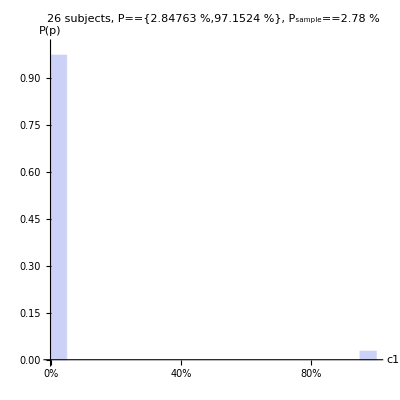

```mathematica
Table[histogram[jj],{jj,testnums}]
```

```mathematica
HistogramList[samples[13],{histbins},"Probability"]
```

{{{0,1/20,1/10,3/20,1/5,1/4,3/10,7/20,2/5,9/20,1/2,11/20,3/5,13/20,7/10,3/4,4/5,17/20,9/10,19/20,1001/1000}},{{0.9722,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0278}}}

```mathematica
samples[13][[1;;10]]
```

{{5.65887503258786×10^-1163},{1.30801867844547×10^-2488},{1.66124226714154×10^-1981},{4.07458410248596×10^-3257},{2.06631061136592×10^-2697},{5.012506343956×10^-1849},{5.36341149693812×10^-1548},{4.33348406457218×10^-1035},{4.83318403737227×10^-3678},{5.80100778372137×10^-1889}}

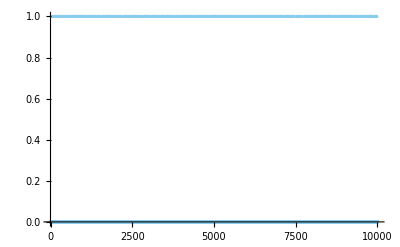

```mathematica
ListPlot[Flatten@samples[13],Joined->False]
```